1)

```mathematica
f[x_]:=Which[0.3≤ x ≤ 0.5,2x-Log[x],0.5≤x≤ 0.8,(2/x)+Abs[x-0.6],True,0]
```

```mathematica
Integrate[f[x],x]
```

Piecewise[{{0., x≤0.3}, {-0.751192+x+x^2-1. x Log[x], 0.3<x≤0.5}, {1.55668+0.6 x-0.5 x^2+2. Log[x], 0.5<x≤0.6}, {1.91668-0.6 x+0.5 x^2+2. Log[x], 0.6<x≤0.8}, {1.31039, True}}]

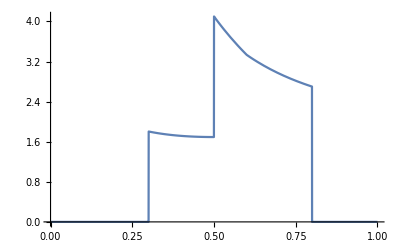

```mathematica
1.310389007473663
Plot[f[x],{x,0,1}]
```

2)

```mathematica
c=Table[Sqrt[Abs[2.3i-2.4j]],{i,4},{j,4}]
```

{{0.316228,1.58114,2.21359,2.70185},{1.48324,0.447214,1.61245,2.23607},{2.12132,1.44914,0.547723,1.64317},{2.60768,2.09762,1.41421,0.632456}}

```mathematica
Eigenvalues[c]
```

{6.31647,-2.46092,-1.17178,-0.740149}

```mathematica
p[a_]:= Max[Abs[Eigenvalues[a]]]
```

```mathematica
p[c]
```

6.31647

```mathematica
N[p[c]]
```

6.31647

3)

```mathematica
x=0
```

0

```mathematica
For[i=1,i≤23,i++,x=x+i^3]
```

```mathematica
x
```

76176

4)

```mathematica
y=1
```

1

```mathematica
For[j=5,j≤21,j++,y=y/j]
```

```mathematica
y
```

1/2128789257154560000

```mathematica
Product[1/(i+4),{i,17}]
```

1/2128789257154560000

5)

Forma recurrente:

```mathematica
g[1]=1
g[2]=1
```

1

1

```mathematica
g[n_]:=g[n-1]+g[n-2]
```

```mathematica
g[10]
g[20]
g[25]
g[30]
g[35]
g[37]
g[39]
```

55

6765

75025

832040

9227465

24157817

63245986

Forma explícita:

```mathematica
f[n_]:=(((1+Sqrt[5])/2)^n-((1-Sqrt[5])/2)^n)/Sqrt[5.]
```

```mathematica
f[10]
```

55.

```mathematica
f[39]
```

6.3246×10^7

6)

```mathematica
a=Table[N[(i-j)/(i+j)],{i,4},{j,4}]
```

{{0.,-0.333333,-0.5,-0.6},{0.333333,0.,-0.2,-0.333333},{0.5,0.2,0.,-0.142857},{0.6,0.333333,0.142857,0.}}

```mathematica
MatrixForm[a]
```

(0. | -0.333333 | -0.5 | -0.6
0.333333 | 0. | -0.2 | -0.333333
0.5 | 0.2 | 0. | -0.142857
0.6 | 0.333333 | 0.142857 | 0.)

```mathematica
normainf[b_]:=
Module[{n},n=Length[b[[1]]];Max[Table[Sum[Abs[b[[i,j]]],{j,n}],{i,n}]]]
```

```mathematica
c=Inverse[IdentityMatrix[4]-a]
```

{{0.61899,-0.334703,-0.274079,-0.220672},{0.0176841,0.86145,-0.219196,-0.266447},{0.253951,-0.00724615,0.835991,-0.269382},{0.413567,0.0852932,-0.118085,0.740298}}

```mathematica
d=Sum[MatrixPower[a,i],{i,0,100}]
```

{{0.620291,-0.33356,-0.273141,-0.219919},{0.0176242,0.861924,-0.218449,-0.265535},{0.253082,-0.00721921,0.836551,-0.268463},{0.412155,0.085,-0.117681,0.741185}}

Error absoluto:

```mathematica
normainf[d-c]
```

0.0041353

Error relativo:

```mathematica
%/normainf[c]
```

0.002855

7)

```mathematica
norma1[b_]:=
normainf[Transpose[b]]
```

```mathematica
a={{0.9,1.1,3.01},{1,-3.2,-2.9},{-3/2,2/5,1.1}}
```

{{0.9,1.1,3.01},{1,-3.2,-2.9},{-3/2,2/5,1.1}}

```mathematica
norma1[a]
```

7.01

8)

```mathematica
condicionamientoMatriz[a_]:=Which[Det[a]≠0,normainf[a]*normainf[Inverse[a]],True,Print["La matriz no es regular"]]
```

```mathematica
a:={{-1,-4,-7},{1,5/2,4},{3,6,9}}
```

```mathematica
b:={{1,1.1,0,-2},{1/7,2/9,1,1},{0.1,-0.4,0.87,3.14},{2.71,0.81,0.82,-2.38}}
```

```mathematica
condicionamientoMatriz[a]
```

La matriz no es regular

```mathematica
condicionamientoMatriz[b]
```

21.9141

9)

```mathematica
radioEspectral[a_]:=Max[Abs[Eigenvalues[a]]]
```

```mathematica
normaEuclidea[x_]:=Sqrt[radioEspectral[a*Transpose[a]]]
```

```mathematica
a=Table[(i+j)/Sqrt[1234.5],{i,3},{j,3}]
```

{{0.0569226,0.0853838,0.113845},{0.0853838,0.113845,0.142306},{0.113845,0.142306,0.170768}}

```mathematica
normaEuclidea[a]
```

0.218641

10)

```mathematica
iterar[a_,y_,n_]:=
For[i=1;x=y,i≤n,i++,x=y+a.x;Print[x]]
```

```mathematica
a=Table[(i+j)/Sqrt[1234.5],{i,3},{j,3}]
```

{{0.0569226,0.0853838,0.113845},{0.0853838,0.113845,0.142306},{0.113845,0.142306,0.170768}}

```mathematica
y={1,2,-1/4}
```

{1,2,-1/4}

```mathematica
iterar[-a,y,10]
```

{0.800771,1.7225,-0.605766}

{0.876308,1.82173,-0.482842}

{0.849541,1.78649,-0.526554}

{0.85905,1.79901,-0.511027}

{0.855672,1.79456,-0.516543}

{0.856872,1.79614,-0.514583}

{0.856446,1.79558,-0.515279}

{0.856597,1.79578,-0.515032}

{0.856543,1.79571,-0.51512}

{0.856562,1.79574,-0.515089}

```mathematica
x=Inverse[(IdentityMatrix[3]+a)].y
```

{0.856557,1.79573,-0.515097}

```mathematica
Max[Abs[x-{0.8565624774870124,1.7957368714706454,-0.5150887345457218}]]≤ normainf[a]^(10+1)*Max[Abs[y]](1-normainf[a])
```

True

```mathematica
Max[Abs[y]]/(1+normainf[a])≤ Max[Abs[x]]
```

True

```mathematica
Max[Abs[y]]/(1-normainf[a])≥   Max[Abs[x]]
```

True

11)

```mathematica
For[i = 1,i≤20,i++,Print[N[Sqrt[5+10^(-i)]-Sqrt[5],15]]]
```

0.0222499806274533

0.00223495106014944

0.000223595618527986

0.000022360567972717

2.23606685946692×10^-6

2.2360678656964×10^-7

2.23606796631945×10^-8

2.23606797638176×10^-9

2.23606797738799×10^-10

2.23606797748861×10^-11

2.23606797749867×10^-12

2.23606797749968×10^-13

2.23606797749978×10^-14

2.23606797749979×10^-15

2.23606797749979×10^-16

2.23606797749979×10^-17

2.23606797749979×10^-18

2.23606797749979×10^-19

2.23606797749979×10^-20

2.23606797749979×10^-21

```mathematica
For[i = 1,i≤20,i++,Print[N[10^(-n)/(Sqrt[5.+10^(-i)]+Sqrt[5.]),10]]]
```

0.2225 10.^(-1. n)

0.223495 10.^(-1. n)

0.223596 10.^(-1. n)

0.223606 10.^(-1. n)

0.223607 10.^(-1. n)

0.223607 10.^(-1. n)

0.223607 10.^(-1. n)

«13 more identical outputs»